Distribution.txt

ErrorList.txt

-Graphics3D-

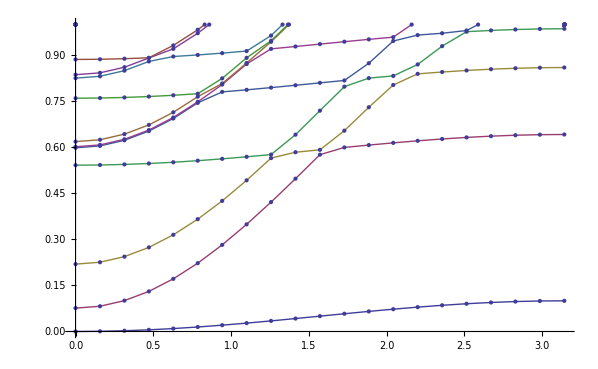

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Get["Methods.m",Path->FileNameJoin[{Directory[],"Packages"}]]

ϵ1=10.;
ϵ2=5.;
H=12.;(*Height of first layer in angstroms*)
a= 3.904;(*unit cell size in angstroms*)
t1=.25;(*hopping parameters in eV*)
t2=.025;
MM=14;
NN=8;
β=.95;(*percent of the old distribution to keep when calculating the new distribution*)
numPartitions=20;
numStates=Ceiling[((ϵ2/ϵ1)(1/2 ArcTan[(MM a)/(2H)]-1/2 ArcTan[-((MM-2) a)/(2H)])NN (MM-1) 1/numPartitions)];

SetParameters[ϵ1,ϵ2,H, a,  t1,t2, MM, NN, β, numPartitions, numStates];
Initialize[];
firstGuess=Flatten[Table[
	 chargeDist[i,j],
	{i,1,NN},
	{j,1,MM-1}
],1];
firstGuess=totalCharge/(firstGuess//Abs//Total)firstGuess;
(*firstGuess=Import["Distribution.txt","List"];*)


{listvals,errorList}=SelfConsistentDistribution[firstGuess,.00005];
Export["Distribution.txt",listvals,"List"]
Export["ErrorList.txt",errorList,"List"]
PlotFullSpaceDistribution[listvals]
bandList=BandStructureList[listvals];
BandStructurePlot[0,1,bandList]
```

```mathematica
firstGuess=Import["Distribution.txt","List"]
```

{-0.00117886,-0.0022986,-0.00330307,-0.00414007,-0.0044687,0.00792916,0.0606942,0.00792916,-0.0044687,-0.00414007,-0.00330307,-0.0022986,-0.00117886,-0.000752575,-0.00146741,-0.00210867,-0.002644,-0.00301761,-0.00204668,0.00285302,-0.00204668,-0.00301761,-0.002644,-0.00210867,-0.00146741,-0.000752575,-0.00048044,-0.000936788,-0.00134616,-0.00168803,-0.00194518,-0.00210164,-0.00214292,-0.00210164,-0.00194518,-0.00168803,-0.00134616,-0.000936788,-0.00048044,-0.00030671,-0.00059804,-0.000859382,-0.00107763,-0.00124184,-0.00134378,-0.00137833,-0.00134378,-0.00124184,-0.00107763,-0.000859382,-0.00059804,-0.00030671,-0.000195802,-0.000381786,-0.000548625,-0.000687954,-0.000792786,-0.000857864,-0.000879926,-0.000857864,-0.000792786,-0.000687954,-0.000548625,-0.000381786,-0.000195802,-0.000124999,-0.00024373,-0.000350239,-0.000439186,-0.00050611,-0.000547656,-0.00056174,-0.000547656,-0.00050611,-0.000439186,-0.000350239,-0.00024373,-0.000124999,-0.0000797986,-0.000155596,-0.000223591,-0.000280374,-0.000323098,-0.00034962,-0.000358612,-0.00034962,-0.000323098,-0.000280374,-0.000223591,-0.000155596,-0.0000797986,-0.000050943,-0.0000993314,-0.000142739,-0.000178989,-0.000206264,-0.000223196,-0.000228936,-0.000223196,-0.000206264,-0.000178989,-0.000142739,-0.0000993314,-0.000050943}